```mathematica
SetDirectory[NotebookDirectory[]];
(* shape functions displacement *)
Nd0[ξ]=1/4(2+ξ)(1-ξ)^2;
Nd1[ξ]=1/4(2-ξ)(1+ξ)^2;
(* shape functions tangent *)
Nt0[ξ]=1/4(1+ξ)(1-ξ)^2;
Nt1[ξ]=-1/4(1-ξ)(1+ξ)^2;
```

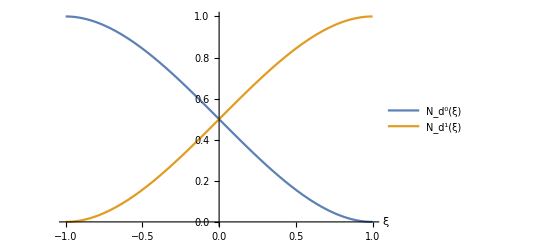

```mathematica
pd = Plot[{Nd0[ξ],Nd1[ξ]},{ξ, -1, 1},AxesLabel->{"ξ", None},PlotRange->{{-1,1},{0,1}}, PlotLegends->{"N_d^0(ξ)", "N_d^1(ξ)"}, LabelStyle->Directive[FontSize->14]]
Export["nd.pdf",pd];
```

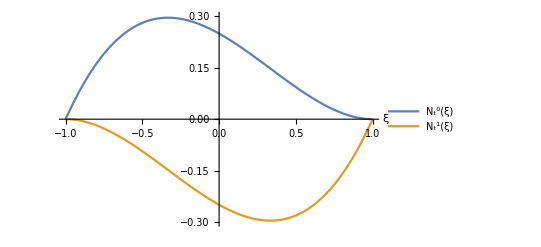

```mathematica
pt = Plot[{Nt0[ξ],Nt1[ξ]},{ξ, -1, 1},AxesLabel->{"ξ", None}, PlotRange->{{-1,1},{-0.3,0.3}},PlotLegends->{"N_t^0(ξ)", "N_t^1(ξ)"}, LabelStyle->Directive[FontSize->14]]
Export["nt.pdf",pt];
```

```mathematica
ud0=0;vd0=0;wd0=0;ut0=1;vt0=0;wt0=0;
ud1=1;vd1=0;wd1=0;ut1=1;vt1=0;wt1=0;
u[ξ]= Nd0[ξ]*ud0 +  Nd1[ξ]*ud1 + 0.5*Nt0[ξ]*ut0 + 0.5*Nt1[ξ]*ut1 ;
v[ξ]= Nd0[ξ]*vd0 +  Nd1[ξ]*vd1 + 0.5*Nt0[ξ]*vt0 + 0.5*Nt1[ξ]*vt1 ;
w[ξ]= Nd0[ξ]*wd0 +  Nd1[ξ]*wd1 + 0.5*Nt0[ξ]*wt0 + 0.5*Nt1[ξ]*wt1 ;
(*Plot[u[ξ], {ξ,-1,1}]*)
(*Plot[v[ξ], {ξ,-1,1}]*)
(*Plot[w[ξ], {ξ,-1,1}]*)
ParametricPlot3D[{u[ξ],v[ξ],w[ξ]} //Evaluate,{ξ, -1,1}]
```

-Graphics3D-